```mathematica
SetDirectory@NotebookDirectory[];
Import["path to QuESTlink.m"];
CreateLocalQuESTEnv["path to quest_link"];
(*Read the paper [Tyson Jones and Simon Benjamin, arXiv:1912.07904] for how to setup the environment.*)
```

## Parameters

```mathematica
numQb=2;
PI=N[π,12];
θ=7PI/16;
Ns=100;
```

## QC

```mathematica
ρIN=CreateDensityQureg[numQb];
ρOUT=CreateDensityQureg[numQb];
ρWP=CreateDensityQureg[numQb];
```

## Memristor Circuit

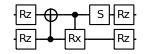

```mathematica
circMR={Subscript[Rz, 0][θ],Subscript[Rz, 1][θ],Subscript[C, 0][Subscript[X, 1]],Subscript[C, 1][Subscript[Rx, 0][PI-2θ]],Subscript[S, 1],Subscript[Rz, 1][-θ],Subscript[Rz, 0][-θ]};
DrawCircuit@circMR
```

## Initialisation Map

```mathematica
P0={{1,0},{0,0}};
SP={{0,1},{0,0}};
INI={P0,SP};
```

## Long-Term Plasticity

```mathematica
ZMlist={0};
InitZeroState[ρIN];
ApplyCircuit[{Subscript[H, 0]},ρIN,ρOUT];ρIN=ρOUT;

(*Long-Term Depression*)
Do[(
circ={Subscript[Kraus, 1][INI],Subscript[X, 1]};
circ=Join[circ,circMR];
ApplyCircuit[circ,ρIN,ρOUT];ρIN=ρOUT;
ZM=CalcExpecPauliSum[ρOUT,Subscript[Z, 0],ρWP];
AppendTo[ZMlist,ZM];
),{i,Ns}];

(*Long-Term Potentiation*)
Do[(
circ={Subscript[Kraus, 1][INI]};
circ=Join[circ,circMR];
ApplyCircuit[circ,ρIN,ρOUT];ρIN=ρOUT;
ZM=CalcExpecPauliSum[ρOUT,Subscript[Z, 0],ρWP];
AppendTo[ZMlist,ZM];
),{i,Ns}];

(*Long-Term Depression*)
Do[(
circ={Subscript[Kraus, 1][INI],Subscript[X, 1]};
circ=Join[circ,circMR];
ApplyCircuit[circ,ρIN,ρOUT];ρIN=ρOUT;
ZM=CalcExpecPauliSum[ρOUT,Subscript[Z, 0],ρWP];
AppendTo[ZMlist,ZM];
),{i,Ns}];

(*Reinitialisation*)
Do[(
circ={Subscript[Kraus, 1][INI],Subscript[H, 1]};
circ=Join[circ,circMR];
ApplyCircuit[circ,ρIN,ρOUT];ρIN=ρOUT;
ZM=CalcExpecPauliSum[ρOUT,Subscript[Z, 0],ρWP];
AppendTo[ZMlist,ZM];
),{i,Ns}];
```

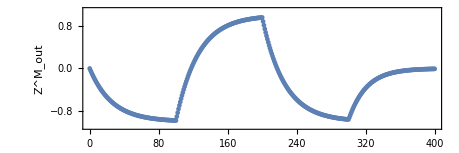

```mathematica
plotS=ListPlot[Transpose[{Range[0,4Ns],ZMlist}],PlotRange->{{0,400},{-1.1,1.1}},Axes->{False,False},Frame->True,FrameLabel->{"Time sequence","Z^M_out"},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->{460,Automatic},LabelStyle->{FontSize->18},AspectRatio->1/3];
plotL=ListLinePlot[Transpose[{Range[0,4Ns],ZMlist}]];
Show[plotS,plotL]
```